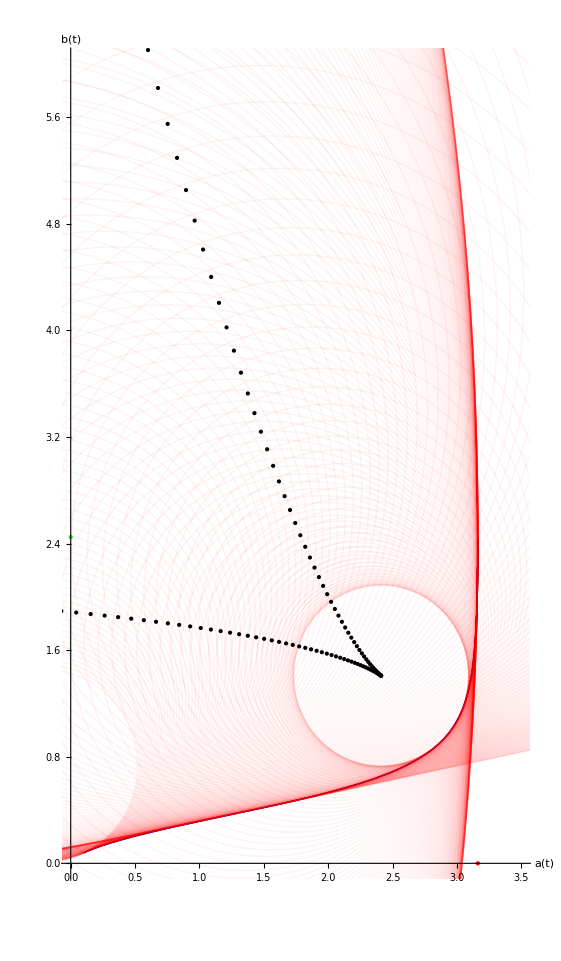

```mathematica
a[t_]:=Sqrt[10] Exp[2*10*t]/Sqrt[1000+Exp[4*10*t]];
b[t_]:=Sqrt[6] Exp[2*6*t]/Sqrt[1000+Exp[4*6*t]];

tValues=Range[0,0.4,0.001];

curvature[t_]:=Abs[(a'[t] b''[t]-a''[t] b'[t])/((a'[t]^2+b'[t]^2)^(3/2))];
radius[t_]:=1/curvature[t];
center[t_]:={a[t]-b'[t] radius[t]/Sqrt[a'[t]^2+b'[t]^2],b[t]+a'[t] radius[t]/Sqrt[a'[t]^2+b'[t]^2]};

Show[ParametricPlot[{a[t],b[t]},{t,0,1},AspectRatio->Automatic,PlotStyle->{Blue,Thick},AxesLabel->{"a(t)","b(t)"},PlotRange->{{0,4},{0,4}}],Graphics[{Red,Opacity[0.05],Circle[center[#],radius[#]]&/@tValues}],Graphics[{Black,PointSize[Medium],Point[center[#]]&/@tValues}],Graphics[{{PointSize[Large],Red,Point[{Sqrt[10],0}]},{PointSize[Large],Green,Point[{0,Sqrt[6]}]}}],PlotRange->{{0,3.5},{0,6}}]
```

```mathematica
N[8/10]
```

0.8

```mathematica
N[1.269/2.902]
```

0.437285

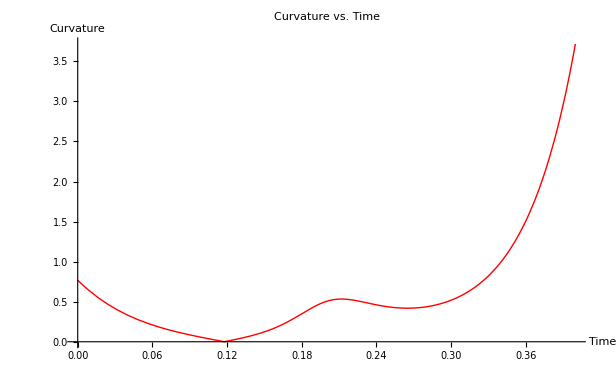

```mathematica
curvaturePlot=Plot[curvature[t],{t,0,0.4},PlotStyle->{Red,Thick},AxesLabel->{"Time","Curvature"},PlotLabel->"Curvature vs. Time",PlotRange->All]
```

```mathematica
curvature[t]
```

Abs[(((432 √6 ⅇ^(60 t))/((1000+ⅇ^(24 t))^(5/2))-(576 √6 ⅇ^(36 t))/((1000+ⅇ^(24 t))^(3/2))+(144 √6 ⅇ^(12 t))/(√(1000+ⅇ^(24 t)))) (-(20 √10 ⅇ^(60 t))/((1000+ⅇ^(40 t))^(3/2))+(20 √10 ⅇ^(20 t))/(√(1000+ⅇ^(40 t))))-(-(12 √6 ⅇ^(36 t))/((1000+ⅇ^(24 t))^(3/2))+(12 √6 ⅇ^(12 t))/(√(1000+ⅇ^(24 t)))) ((1200 √10 ⅇ^(100 t))/((1000+ⅇ^(40 t))^(5/2))-(1600 √10 ⅇ^(60 t))/((1000+ⅇ^(40 t))^(3/2))+(400 √10 ⅇ^(20 t))/(√(1000+ⅇ^(40 t)))))/((-(12 √6 ⅇ^(36 t))/((1000+ⅇ^(24 t))^(3/2))+(12 √6 ⅇ^(12 t))/(√(1000+ⅇ^(24 t))))^2+(-(20 √10 ⅇ^(60 t))/((1000+ⅇ^(40 t))^(3/2))+(20 √10 ⅇ^(20 t))/(√(1000+ⅇ^(40 t))))^2)^(3/2)]